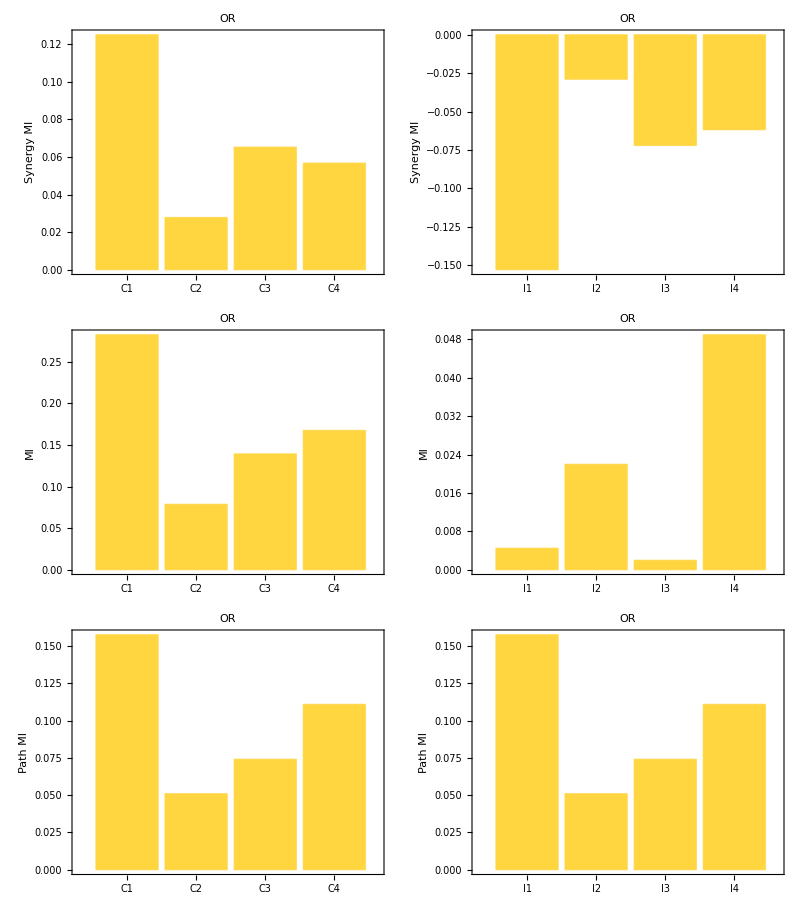

```mathematica
(*
Notations: xav=<x>, yav=<y>, zav=<z>
		fijp=Subscript[f, ij]'
*)
(*------Squared coefficient of variation: Subscript[CV^2, i]=Subscript[σ^2, i]/(<i>^2), Subscript[CV^2, ij]=Subscript[σ^2, ij]/(<i><j>)------*)

Γxy=1/(βx+βy);
Γxz=1/(βx+βz);
Γyz=1/(βy+βz);
Γxyz1=1/((βx+βy)*(βx+βz));
Γxyz2=(βx+βy+βz)/(βy*(βx+βy)*(βx+βz)*(βy+βz));
Γxyz3=(2*βx+βy+βz)/((βx+βy)*(βx+βz)*(βy+βz));



ηxy=Γxy/yav*fyxp; (*Subscript[η^2, xy]*)

ηxz1=Γxz/zav*fzxp; (*Subscript[η^2, xz,d]*)
ηxz2=Γxyz1/zav*fyxp*fzyp; (*Subscript[η^2, xz,ind]*)

ηxz=ηxz1+ηxz2; (*Subscript[η^2, xz]*)

ηyz1=Γyz/zav*fzyp; (*Subscript[η^2, yz,Subscript[ind, 1]]*)
ηyz2=(Γxyz2*xav)/(yav*zav)*fyxp^2*fzyp; (*Subscript[η^2, yz,Subscript[ind, 2]]*)
ηyz3=(Γxyz3*xav)/(yav*zav)*fyxp*fzxp; (*Subscript[η^2, yz,cross]*)
ηyz=ηyz1+ηyz2+ηyz3; (*Subscript[η^2, yz]*)


ηx=1/xav;

ηy=1/yav+(fyxp^2*xav)/(βy*yav)*ηxy;

ηzi=1/zav; (*Subscript[η^2, z,int]*)

ηzd=(fzxp*xav)/(βz*zav)*ηxz1; (*Subscript[η^2, z,d]*)

ηzind=(fzyp*yav)/(βz*zav)*(ηyz1+ηyz2); (*Subscript[η^2, z,ind]*)

prefactor1=(fzxp*xav)/(βz*zav);
ηzsyn1=prefactor1*ηxz2; 
prefactor2=(fzyp*yav)/(βz*zav);
ηzsyn2=prefactor2*ηyz3; 
ηzsyn=ηzsyn1+ηzsyn2; (*Subscript[η^2, z,cross]*)

ηp=ηzi+ηzd+ηzind; (*Subscript[η^2, z,path]*)

ηz=ηp+ηzsyn; (*Subscript[η^2, z]*)

ηr=ηzsyn/ηp; (*Relative synergy noise*)


(*Entropy Gain*)
Hz=1/2*Log2[2*Pi*Exp[1]*zav^2*ηz];

Hz0=1/2*Log2[2*Pi*Exp[1]*zav^2*ηp];
Hzs=1/2*Log2[1+ηzsyn/ηp];


(** Information XY->Z **)

Ixz=1/2*Log2[(ηx*ηz)/(ηx*ηz-ηxz^2)];

Ixz0=1/2*Log2[ηp/(ηp-(ηxz1^2+ηxz2^2)/ηx)];
Ixzs=1/2*Log2[(1+ηzsyn/ηp)/(1+(ηzsyn-(2*ηxz1*ηxz2)/ηx)/(ηp-(ηxz1^2+ηxz2^2)/ηx))];



Df=(2*ηxz1*ηxz2)/ηx;

Eyx =(xav*fyxpp)/fyx;
Ezx =(xav*fzxpp)/fzx;
Ezy =(yav*fzypp)/fzy;
Ed=Ezx;
Ei=Eyx*Ezy;

(*------Particular motifs and their functions------*)


(*##################################################*)

(*C1FFL-OR*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=0.1; βy=1.0; βz=10.0;
xav=40; yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=100;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx+fzy);
fyx=xav/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*Kxz/(Kxz+xav)^2; fzyp=αz*Kyz/(Kyz+yav)^2;
fyxpp=Kxy/(Kxy+xav)^2;fzxpp=Kxz/(Kxz+xav)^2; fzypp=Kyz/(Kyz+yav)^2;

Isc1ae=Ixzs;
Ic1ae=Ixz;
I0c1ae=Ixz0;


(*C2FFL-OR*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=0.1; βy=1.0; βz=10.0;
xav=40; yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=100;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx+fzy);
fyx=Kxy/(Kxy+xav); fzx=Kxz/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*-Kxy/(Kxy+xav)^2;fzxp=αz*-Kxz/(Kxz+xav)^2; fzyp=αz*Kyz/(Kyz+yav)^2;
fyxpp=-Kxy/(Kxy+xav)^2;fzxpp=-Kxz/(Kxz+xav)^2; fzypp=Kyz/(Kyz+yav)^2;

Isc2ae=Ixzs; 
Ic2ae=Ixz;
I0c2ae=Ixz0;


(*C3FFL-OR*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=0.1; βy=1.0; βz=10.0;
xav=40; yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=100;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx+fzy);
fyx=xav/(Kxy+xav); fzx=Kxz/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*-Kxz/(Kxz+xav)^2; fzyp=αz*-Kyz/(Kyz+yav)^2;
fyxpp=Kxy/(Kxy+xav)^2;fzxpp=-Kxz/(Kxz+xav)^2; fzypp=-Kyz/(Kyz+yav)^2;


Isc3ae=Ixzs; 
Ic3ae=Ixz;
I0c3ae=Ixz0;


(*C4FFL-OR*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=0.1; βy=1.0; βz=10.0;
xav=40; yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=100;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx+fzy);
fyx=Kxy/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*-Kxy/(Kxy+xav)^2;fzxp=αz*Kxz/(Kxz+xav)^2; fzyp=αz*-Kyz/(Kyz+yav)^2;
fyxpp=-Kxy/(Kxy+xav)^2;fzxpp=Kxz/(Kxz+xav)^2; fzypp=-Kyz/(Kyz+yav)^2;


Isc4ae=Ixzs; 
Ic4ae=Ixz;
I0c4ae=Ixz0;



(*##################################################*)

(*I1FFL-OR*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=0.1; βy=1.0; βz=10.0;
xav=40; yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=100;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx+fzy);
fyx=xav/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*Kxz/(Kxz+xav)^2; fzyp=αz*-Kyz/(Kyz+yav)^2;
fyxpp=Kxy/(Kxy+xav)^2;fzxpp=Kxz/(Kxz+xav)^2; fzypp=-Kyz/(Kyz+yav)^2;

Isi1ae=Ixzs; 
Ii1ae=Ixz;
I0i1ae=Ixz0;


(*I2FFL-OR*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=0.1; βy=1.0; βz=10.0;
xav=40; yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=100;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx+fzy);
fyx=Kxy/(Kxy+xav); fzx=Kxz/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*-Kxy/(Kxy+xav)^2;fzxp=αz*-Kxz/(Kxz+xav)^2; fzyp=αz*-Kyz/(Kyz+yav)^2;
fyxpp=-Kxy/(Kxy+xav)^2;fzxpp=-Kxz/(Kxz+xav)^2; fzypp=-Kyz/(Kyz+yav)^2;

Isi2ae=Ixzs; 
Ii2ae=Ixz;
I0i2ae=Ixz0;

(*I3FFL-OR*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=0.1; βy=1.0; βz=10.0;
xav=40; yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=100;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx+fzy);
fyx=xav/(Kxy+xav); fzx=Kxz/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*Kxy/(Kxy+xav)^2;fzxp=αz*-Kxz/(Kxz+xav)^2; fzyp=αz*Kyz/(Kyz+yav)^2;
fyxpp=Kxy/(Kxy+xav)^2;fzxpp=-Kxz/(Kxz+xav)^2; fzypp=Kyz/(Kyz+yav)^2;

Isi3ae=Ixzs; 
Ii3ae=Ixz;
I0i3ae=Ixz0;


(*I4FFL-OR*)
Clear[βx,βy,βz,xav,yav,zav,Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,fyxpp,fzxpp,fzypp];

βx=0.1; βy=1.0; βz=10.0;
xav=40; yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=100;

αy= (βy*yav)/fyx; αz=(βz*zav)/(fzx+fzy);
fyx=Kxy/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*-Kxy/(Kxy+xav)^2;fzxp=αz*Kxz/(Kxz+xav)^2; fzyp=αz*Kyz/(Kyz+yav)^2;
fyxpp=-Kxy/(Kxy+xav)^2;fzxpp=Kxz/(Kxz+xav)^2; fzypp=Kyz/(Kyz+yav)^2;

Isi4ae=Ixzs;
Ii4ae=Ixz;
I0i4ae=Ixz0;

(*Plots*)
p1=BarChart[{Isc1ae,Isc2ae,Isc3ae,Isc4ae},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"","Synergy MI"},ImageSize->300,ChartLabels->{"C1","C2","C3","C4"},PlotLabel->"OR"];

p2=BarChart[{Isi1ae,Isi2ae,Isi3ae,Isi4ae},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"","Synergy MI"},ImageSize->300,ChartLabels->{"I1","I2","I3","I4"},PlotLabel->"OR"];

p3=BarChart[{Ic1ae,Ic2ae,Ic3ae,Ic4ae},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"","MI"},ImageSize->300,ChartLabels->{"C1","C2","C3","C4"},PlotLabel->"OR"];

p4=BarChart[{Ii1ae,Ii2ae,Ii3ae,Ii4ae},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"","MI"},ImageSize->300,ChartLabels->{"I1","I2","I3","I4"},PlotLabel->"OR"];

p5=BarChart[{I0c1ae,I0c2ae,I0c3ae,I0c4ae},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"","Path MI"},ImageSize->300,ChartLabels->{"C1","C2","C3","C4"},PlotLabel->"OR"];

p6=BarChart[{I0i1ae,I0i2ae,I0i3ae,I0i4ae},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"","Path MI"},ImageSize->300,ChartLabels->{"I1","I2","I3","I4"},PlotLabel->"OR"];

Grid[{{p1,p2},{p3,p4},{p5,p6}}]


(*Define your labels*)
labelsc={"C1","C2","C3","C4"};
labelsi={"I1","I2","I3","I4"};

toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];


(*Define your data*)
values={Isc1ae,Isc2ae,Isc3ae,Isc4ae};
formattedValues=toEString/@values;
t1=Transpose[{labelsc,formattedValues}];
Export["F:\\Colab\\FFL-Info-Decomp\\Theory\\non-CEM-IMI\\IMI-coherent-OR.dat",t1,"Table"];

values={Isi1ae,Isi2ae,Isi3ae,Isi4ae};
formattedValues=toEString/@values;
t2=Transpose[{labelsi,formattedValues}];
Export["F:\\Colab\\FFL-Info-Decomp\\Theory\\non-CEM-IMI\\IMI-incoherent-OR.dat",t2,"Table"];


values={Ic1ae,Ic2ae,Ic3ae,Ic4ae};
formattedValues=toEString/@values;
t3=Transpose[{labelsc,formattedValues}];
Export["F:\\Colab\\FFL-Info-Decomp\\Theory\\non-CEM-IMI\\MI-coherent-OR.dat",t3,"Table"];

values={Ii1ae,Ii2ae,Ii3ae,Ii4ae};
formattedValues=toEString/@values;
t4=Transpose[{labelsi,formattedValues}];
Export["F:\\Colab\\FFL-Info-Decomp\\Theory\\non-CEM-IMI\\MI-incoherent-OR.dat",t4,"Table"];



values={I0c1ae,I0c2ae,I0c3ae,I0c4ae};
formattedValues=toEString/@values;
t5=Transpose[{labelsc,formattedValues}];
Export["F:\\Colab\\FFL-Info-Decomp\\Theory\\non-CEM-IMI\\PMI-coherent-OR.dat",t5,"Table"];

values={I0i1ae,I0i2ae,I0i3ae,I0i4ae};
formattedValues=toEString/@values;
t6=Transpose[{labelsi,formattedValues}];
Export["F:\\Colab\\FFL-Info-Decomp\\Theory\\non-CEM-IMI\\PMI-incoherent-OR.dat",t6,"Table"];

Quit[];
```